```mathematica
Clear["Global`*"]
```

```mathematica
q2=(1+0.1Cos[5t])Cos[100t];
```

```mathematica
q2ex=Expand[q2]
```

```mathematica
Cos[100 t]+0.1 Cos[5 t] Cos[100 t]
```

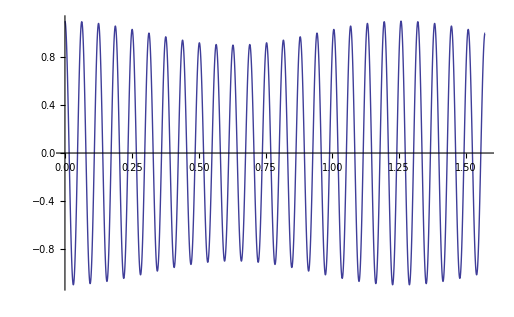

```mathematica
Plot[Evaluate[q2],{t,0,π/2}]
```

```mathematica
q2identPoS=Cos[100t]+0.1(1/2(Cos[100t-5t]+Cos[100t+5t]))
```

Cos[100 t]+0.05 (Cos[95 t]+Cos[105 t])

```mathematica
Cos[x]==Sin[x+π/2];
```

```mathematica
Sin[100t+π/2]+0.05(Sin[95t+π/2]+Sin[105t+π/2]);
0.05Sin[95t+π/2]+Sin[100t+π/2]+0.05Sin[105t+π/2];
```

```mathematica
q2sin1=0.05Sin[95t+π/2];
q2sin2=Sin[100t+π/2];
q2sin3=0.05Sin[105t+π/2];
```

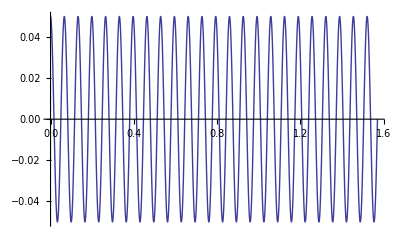

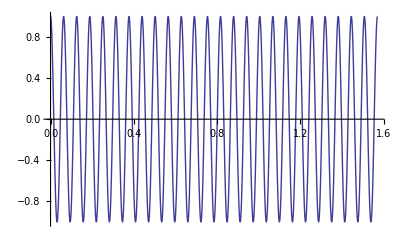

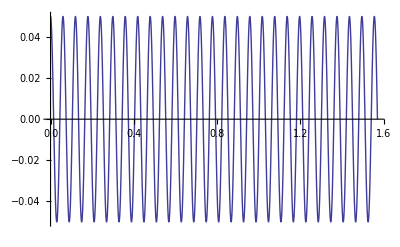

```mathematica
Plot[Evaluate[q2sin1],{t,0,π/2}]
Plot[Evaluate[q2sin2],{t,0,π/2}]
Plot[Evaluate[q2sin3],{t,0,π/2}]
```

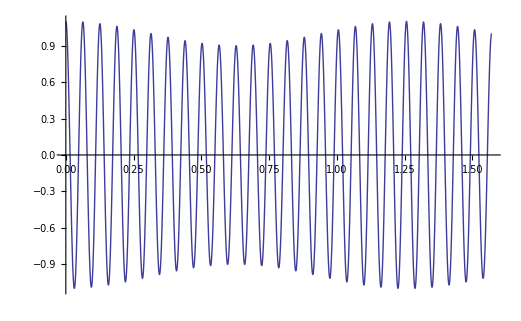

```mathematica
Plot[Evaluate[q2sin1+q2sin2+q2sin3],{t,0,π/2}]
```

```mathematica
1.544×10^6 bps=1×10^6 Hz×Log[2,1+SNR]

(1.544×10^6)/(1×10^6)=Log[2,1+SNR]

1.544=Log[2,1+SNR]

2^1.544=1+SNR

SNR=2^1.544-1
```

```mathematica
SNR=2^1.544-1
```

1.91602

```mathematica
Subscript[SNR, db]=10Log[10,SNR]
```

2.824

```mathematica
Subscript[SNR, db]=2.8239975646314046
```

2.824

```mathematica
BitRate=2×(10×10^3 Hz)×Log[2,16]
```

80000 Hz

```mathematica
BitRate=80000bps==80kbps
```

```mathematica
SamplingRate = 4000×2=8000 samples/s
```

```mathematica
BitRate=8000×8=64000bps=64kbps
```

```mathematica
(45×10^6 bps)/(64×10^3 bps)=703.125~=703
```

```mathematica
Bandwidth=(1+d)×S

S=(2×H×Log[2,8])×(1/3)
```

```mathematica
Subscript[N, max]=2×H×Log[2,L]

Subscript[N, max]=2×H×Log[2,8]
```

```mathematica
BitRate=44.1×10^3×16=705600bps
```

```mathematica
705600bps×(60s)/m=42336000 bpm
```

```mathematica
1gigabyte = 10^9 bytes*(8bits)/byte=8000000000bits
```

```mathematica
(8000000000bits)/(42336000 bpm)=188.9644746787604 ~=188 Songs
```

```mathematica
188.9644746787604/3
```

62.9882

```mathematica
BitRate=Subscript[Pixels, x]×Subscript[Pixels, y]×Depth×Frames
```

```mathematica
BitRate=480×500×6×25=36000000bps
```

36000000

```mathematica
Subscript[SNR, db]=35=10Log[10,SNR]
```

```mathematica
35/10=3.5=Log[10,SNR]
```

```mathematica
SNR=10^3.5=3162.2776601683795
```

```mathematica
Capacity=4.5×10^6×Log[2,10^3.5]=52320400bps
```

```mathematica
6*25
```

150

```mathematica
2^6
```

64